# Create an LLM kernel

## Initialization

```mathematica
Needs[ "Wolfram`Chatbook`" ];
```

## Basic implementation

```mathematica
prompt="I want you to act as a Wolfram Language kernel that gives outputs for the inputs that I enter. You should only reply with Wolfram kernel output and nothing else. I will enter inputs in the following format:
```
In[n]:= <input>
```
You will respond in the following format:
```
Out[n]= <output>
```
For example, if I enter:
```
In[1]:= Table[i^2, {i, 1, 5}]
```
You will respond with:
```
Out[1]= {1, 4, 9, 16, 25}
```
If there are messages printed during the evaluation, include them before the output (separated by two new line characters) in the following format:
```
During evaluation of In[n]:= <message1>

During evaluation of In[n]:= <message2>

Out[n]= <output>
```
If there is no output, return Null.
";
```

```mathematica
CreateChatNotebook[
{Cell[prompt,"ChatSystemInput"],Cell["","ChatInput"]},
"LLMEvaluator"->"RawModel",
WindowMargins->0,WindowSize->{1920,1000},Magnification->2
]
```

### Embed prompt in notebook instead of a cell

```mathematica
CreateChatNotebook[
"Prompts"->prompt,
"LLMEvaluator"->"RawModel",
WindowMargins->0,WindowSize->{1920,1000},Magnification->2
]
```

### Add custom decoration

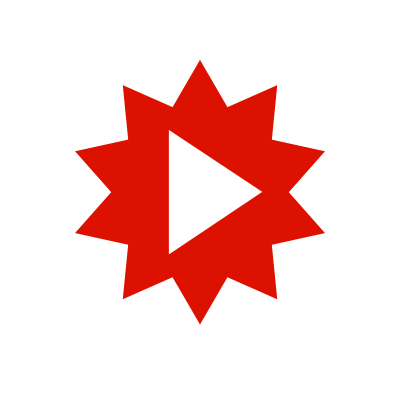
```mathematica
evaluator=<|"Name"->"WolframKernel","Icon"->-Graphics-,"Tools"->None,"BasePrompt"->None|>;
```

```mathematica
CreateChatNotebook[
"Prompts"->prompt,
"LLMEvaluator"->evaluator,
WindowMargins->0,WindowSize->{1920,1000},Magnification->2
]
```

### Stylesheet customization

Any cell type can be used as a chat input—here we hook up regular input cells to ChatCellEvaluate:

```mathematica
stylesheet=Notebook[{
Cell[StyleData[StyleDefinitions->"Chatbook.nb"]],
Cell[StyleData["Input"],CellEvaluationFunction->((ChatCellEvaluate[];)&)]
},
StyleDefinitions->"PrivateStylesheetFormatting.nb"
];
```

```mathematica
CreateChatNotebook[
{Cell[BoxData[""],"Input"]},
"Prompts"->prompt,
"LLMEvaluator"->evaluator,
StyleDefinitions->stylesheet,
WindowMargins->0,WindowSize->{1920,1000},Magnification->2
]
```

### Custom processing functions

#### WriteChatOutputCell

##### Definitions

```mathematica
writeEvaluatorOutput[ target_CellObject, cell_Cell, info_ ] :=
	NotebookWrite[ target, makeOutputCells @ info[ "Result" ] ];
```

```mathematica
makeOutputCells[ string_String ] :=
	makeOutputCell /@ StringTrim @ StringSplit[
		StringDelete[ string, "```" ],
		"\n\n"
	];
```

```mathematica
makeOutputCell[ string_String ] /; 
	StringStartsQ[ string, "Out[" ~~ DigitCharacter.. ~~ "]=" ] := 
    Cell[
        BoxData @ StringDelete[
            string,
            StartOfString ~~ "Out[" ~~ DigitCharacter.. ~~ "]=" ~~ WhitespaceCharacter..
        ],
        "Output",
        CellLabel ->
            StringJoin[
                "Out[",
                First @ StringCases[ string, "Out[" ~~ n: DigitCharacter.. ~~ "]=" :> n ],
                "]="
            ]
    ];
```

```mathematica
makeOutputCell[ string_String ] /;
    StringStartsQ[ string, "During evaluation of In[" ~~ DigitCharacter.. ~~ "]:=" ] := 
    Cell[
        StringTrim @ StringDelete[ 
            string,
            StartOfString ~~ "During evaluation of In[" ~~ DigitCharacter.. ~~ "]:=" 
        ],
        "Message",
        CellLabel -> First @ StringCases[
            string,
            "During evaluation of In[" ~~ DigitCharacter.. ~~ "]:="
        ]
    ];
```

```mathematica
makeOutputCell[ string_String ] := Cell[ string, "Program" ];
```

##### Create chat notebook

```mathematica
CreateChatNotebook[
"Prompts"->prompt,
"LLMEvaluator"->evaluator,
"InitialChatCell"->False,
"ProcessingFunctions"-><|"WriteChatOutputCell"->writeEvaluatorOutput|>,
StyleDefinitions->stylesheet,
WindowMargins->0,WindowSize->{1920,1000},Magnification->2
]
```

#### FormatChatOutput

```mathematica
CreateChatNotebook[
"Prompts"->prompt,
"LLMEvaluator"->evaluator,
"InitialChatCell"->False,
"ProcessingFunctions"-><|
"WriteChatOutputCell"->writeEvaluatorOutput,
"FormatChatOutput"->Function@
If[#2["Status"]==="Streaming",Column[{"Computing stuff...",ProgressIndicator[Appearance->"Indeterminate"]}],
#1
]
|>,
StyleDefinitions->stylesheet,
WindowMargins->0,WindowSize->{1920,1000},Magnification->2
]
```